# Define MPO and Ham

```mathematica
(*n=1,return W_1; n=NN, return W_N; otherwise return W_i*)
isingMPO[h_,n_]:=Module[{sx,sy,sz,si,W},
sx={{0,1.},{1.,0}}/2;
sy={{0,-1.},{1.,0}}/2;
sz={{1.,0},{0,-1.}}/2;
si={{1.,0},{0,1.}};
If[n==1,
W=Table[0,{1},{3},{2},{2}];
W[[1,1]]=-h sz;
W[[1,2]]=sx;
W[[1,3]]=si,
If[n==NN,
W=Table[0,{3},{1},{2},{2}];
W[[1,1]]=si;
W[[2,1]]=-J sx;
W[[3,1]]=-h sz,
W=Table[0,{3},{3},{2},{2}];
W[[1,1]]=si;
W[[2,1]]=-J sx;
W[[3,1]]=-h sz;
W[[3,2]]=sx;
W[[3,3]]=si;
]];

Return[W]
];

(*for iDMRG, return a N=2 Ham*)
isingh1[h_]:=Module[{sx,sy,sz,si},
sx={{0,1.},{1.,0}}/2;
sy={{0,-1.},{1.,0}}/2;
sz={{1.,0},{0,-1.}}/2;
si={{1.,0},{0,1.}};

Return[-J KroneckerProduct[sx,sx]-h KroneckerProduct[sz,si]-h KroneckerProduct[si,sz]]
];

(*setup a random MPS*)
randomMPS[]:=Module[{mps},
mps=Table[RandomReal[],{NN},{d},{DD},{DD}];
mps[[NN]]=Table[RandomReal[],{d},{DD},{1}];
mps[[1]]=Table[RandomReal[],{d},{1},{DD}];

Return[mps]
];

(*bring the random MPS into right normalized form*)
rightNormalize[mps_]:=Module[{Bs,dleft,dright,mmatrix,U,S,V,dimS,mu,norm},
Bs=mps;
Do[dleft=Dimensions[Bs[[i]]][[2]];
dright=Dimensions[Bs[[i]]][[3]];
mmatrix=ArrayReshape[Transpose[Bs[[i]]],{dleft,dright d}];(*transpose the first two index*)
{U,S,V}=SingularValueDecomposition[mmatrix,Min[Dimensions[mmatrix][[2]],DD]];
dimS=Dimensions[S][[1]];
Bs[[i]]=Transpose[ArrayReshape[V†,{dimS,d,dright}]];
mu=Activate @ TensorContract[Inactive[TensorProduct][Bs[[i-1]],U],{3,4}];
Bs[[i-1]]=Activate @ TensorContract[Inactive[TensorProduct][mu,S],{3,4}]
,{i,NN,2,-1}];
norm=Bs[[1,1]].Transpose[Bs[[1,1]]]+Bs[[1,2]].Transpose[Bs[[1,2]]];
(*norm={{1}};*)
Bs[[1]]=Bs[[1]]/√norm[[1,1]];

Return[Bs]
];
```

# MPS Function Main Part

```mathematica
(*isGS=1 for the ground state calculation, other value does not work;
iDMRG=False for a random initial state, otherwise the initial state will build from iDMRG*)
fDMRG[h_,isGS_,iDMRGM_]:=Module[{sz,sx,sy,EGS,M,Mz,Mxx,R,L,Rtmp,heff,heffmat,dim,mlvect,mlmat,U,S,V,dleft,dright},
If[iDMRGM,{EGS,M}=iDMRG[h,isGS],M=rightNormalize[randomMPS[]]];
Mz=Table[Null,{NN}];
Mxx=Table[Null,{NN-1}];
sz={{1.,0},{0,-1.}};
sx={{0,1.},{1.,0}};
sy={{0,-1.},{1.,0}};

R=Table[Null,{NN-1}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][M[[NN]],MPO[h,NN]],{1,7}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][Rtmp,Conjugate[M[[NN]]]],{5,6}];
Rtmp=Transpose[Rtmp,{4,1,5,2,6,3}][[1,1,1]];
R[[NN-1]]=Rtmp;

Do[
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][R[[l+1]],M[[l+1]]],{1,6}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][Rtmp,MPO[h,l+1]],{{1,6},{3,8}}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][Rtmp,Conjugate[M[[l+1]]]],{{1,7},{4,5}}];
R[[l]]=Rtmp
,{l,NN-2,1,-1}];

L=Table[Null,{NN-1}];

Do[
Do[
If[l==1,
heff=Activate @ TensorContract[Inactive[TensorProduct][MPO[h,l],R[[l]]],{2,6}];
heff=ArrayReshape[heff,Insert[Dimensions[heff],1,1]],
heff=Activate @ TensorContract[Inactive[TensorProduct][L[[l-1]],MPO[h,l]],{2,4}];
heff=Activate @ TensorContract[Inactive[TensorProduct][heff,R[[l]]],{3,7}]
];

dim=Dimensions[heff];
heffmat=ArrayReshape[Transpose[heff,{5,2,1,4,6,3}],{dim[[2]] dim[[3]] dim[[6]],dim[[1]] dim[[4]] dim[[5]]}];
dim=Dimensions[M[[l]]];
mlvect=ArrayReshape[M[[l]],{dim[[1]] dim[[2]] dim[[3]]}];

If[isGS==1,
{EGS,mlvect}=Eigensystem[-heffmat,1,Method->{"Arnoldi","Criteria"->"RealPart","StartingVector"->mlvect}];
EGS=-EGS[[1]];
mlvect=mlvect[[1]],
{EGS,mlvect}=Eigensystem[-heffmat,2,Method->{"Arnoldi","Criteria"->"RealPart","StartingVector"->mlvect}];
EGS=-EGS[[2]];
mlvect=mlvect[[2]]
];

mlmat=ArrayReshape[mlvect,{dim[[1]] dim[[2]],dim[[3]]}];
{U,S,V}=SingularValueDecomposition[mlmat,Min[Dimensions[mlmat][[1]],Dimensions[mlmat][[2]],DD]];
If[l==1&&isweep==sweep,Mz[[l]]=opexpval[M[[l]],sz]];
If[l==1&&isweep==sweep,Mxx[[l]]=opexpval2[M,sx,sx,l,l+1]];

dim=Dimensions[S][[1]];
M[[l]]=ArrayReshape[U,{Dimensions[M[[l]]][[1]],Dimensions[M[[l]]][[2]],dim}];
M[[l+1]]=Activate @ TensorContract[Inactive[TensorProduct][V†,M[[l+1]]],{2,4}];
M[[l+1]]=Transpose[Activate @ TensorContract[Inactive[TensorProduct][S,M[[l+1]]],{2,3}]];

If[l==1,
L[[l]]=Activate @ TensorContract[Inactive[TensorProduct][M[[l]],MPO[h,l]],{1,7}];
L[[l]]=Activate @ TensorContract[Inactive[TensorProduct][L[[l]],Conjugate[M[[l]]]],{5,6}];
L[[l]]=Transpose[L[[l]],{1,4,2,5,3,6}][[1,1,1]],
L[[l]]=Activate @ TensorContract[Inactive[TensorProduct][L[[l-1]],M[[l]]],{1,5}];
L[[l]]=Activate @ TensorContract[Inactive[TensorProduct][L[[l]],MPO[h,l]],{{1,5},{3,8}}];
L[[l]]=Activate @ TensorContract[Inactive[TensorProduct][L[[l]],Conjugate[M[[l]]]],{{1,6},{4,5}}]
]
,{l,1,NN-1}];
(*Print[isweep];*)
Do[
If[l==NN,
heff=Activate @ TensorContract[Inactive[TensorProduct][L[[l-1]],MPO[h,l]],{2,4}];
heff=Transpose[heff,{5,3,1,2,4}][[1]];
dim=Dimensions[heff];
heffmat=ArrayReshape[heff,{dim[[1]] dim[[2]],dim[[3]] dim[[4]]}],
heff=Activate @ TensorContract[Inactive[TensorProduct][L[[l-1]],MPO[h,l]],{2,4}];
heff=Activate @ TensorContract[Inactive[TensorProduct][heff,R[[l]]],{3,7}];
dim=Dimensions[heff];
heffmat=ArrayReshape[Transpose[heff,{5,2,1,4,6,3}],{dim[[2]] dim[[3]] dim[[6]],dim[[1]] dim[[4]] dim[[5]]}]
];

dim=Dimensions[M[[l]]];
mlvect=ArrayReshape[M[[l]],{dim[[1]] dim[[2]] dim[[3]]}];

If[isGS==1,
{EGS,mlvect}=Eigensystem[-heffmat,1,Method->{"Arnoldi","Criteria"->"RealPart","StartingVector"->mlvect}];
EGS=-EGS[[1]];
mlvect=mlvect[[1]],
{EGS,mlvect}=Eigensystem[-heffmat,2,Method->{"Arnoldi","Criteria"->"RealPart","StartingVector"->mlvect}];
EGS=-EGS[[2]];
mlvect=mlvect[[2]]
];

M[[l]]=ArrayReshape[mlvect,dim];
dleft=Dimensions[M[[l]]][[2]];
dright=Dimensions[M[[l]]][[3]];
mlmat=ArrayReshape[Transpose[M[[l]]],{dleft,dright d}];
{U,S,V}=SingularValueDecomposition[mlmat,Min[Dimensions[mlmat][[1]],Dimensions[mlmat][[2]],DD]];
If[isweep==sweep,Mz[[l]]=opexpval[M[[l]],sz]];
If[l+1≤NN&&isweep==sweep,Mxx[[l]]=opexpval2[M,sx,sx,l,l+1]];

dim=Dimensions[S][[1]];
M[[l]]=Transpose[ArrayReshape[V†,{dim,d,dright}]];
M[[l-1]]=Activate @ TensorContract[Inactive[TensorProduct][M[[l-1]],U],{3,4}];
M[[l-1]]=Activate @ TensorContract[Inactive[TensorProduct][M[[l-1]],S],{3,4}];

If[l==NN,
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][M[[l]],MPO[h,l]],{1,7}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][Rtmp,Conjugate[M[[l]]]],{5,6}];
Rtmp=Transpose[Rtmp,{4,1,5,2,6,3}][[1,1,1]];
R[[l-1]]=Rtmp,
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][R[[l]],M[[l]]],{1,6}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][Rtmp,MPO[h,l]],{{1,6},{3,8}}];
Rtmp=Activate @ TensorContract[Inactive[TensorProduct][Rtmp,Conjugate[M[[l]]]],{{1,7},{4,5}}];
R[[l-1]]=Rtmp
];

,{l,NN,2,-1}]
,{isweep,1,sweep}];

Return[{EGS,Mxx,Mz}]
];
```

# iDMRG

```mathematica
iDMRG[h_,isGS_]:=Module[{M,SS,L,R,mpo,mpo1,mpo2,MMPO,heff,MA,MB,ΛL,ΛR,ψinit,ψ,ε,EGS,U,S,V,dim,dims},
M=Table[Null,{NN}];
SS=Table[Null,{NN}];
mpo=MPO[h,2];
mpo1=MPO[h,1];
mpo2=MPO[h,NN];
MMPO=Activate @ TensorContract[Inactive[TensorProduct][mpo,mpo],{2,5}];

(*initial two sites*)
{ε,ψ}=Eigensystem[h1[h]];
{ε,ψ}={ε[[#]],ψ[[#]]}&@Ordering[ε];
ψ=ArrayReshape[ψ[[2-isGS]],{d,d}];
{U,S,V}=SingularValueDecomposition[ψ];
M[[1]]=ArrayReshape[U,{d,1,d}];
M[[-1]]=Transpose[ArrayReshape[V†,{d,d,1}]];
SS[[1]]=S;
L=Activate @ TensorContract[Inactive[TensorProduct][M[[1]],mpo1],{1,7}];
L=Activate @ TensorContract[Inactive[TensorProduct][L,Conjugate[M[[1]]]],{5,6}];
L=Transpose[L,{1,4,2,5,3,6}][[1,1,1]];
R=Activate @ TensorContract[Inactive[TensorProduct][M[[-1]],mpo2],{1,7}];
R=Activate @ TensorContract[Inactive[TensorProduct][R,Conjugate[M[[-1]]]],{5,6}];
R=Transpose[R,{4,1,5,2,6,3}][[1,1,1]];

(*initial four sites*)
heff=Activate @ TensorContract[Inactive[TensorProduct][L,MMPO],{2,4}];
heff=Activate @ TensorContract[Inactive[TensorProduct][heff,R],{5,9}];
heff=Transpose[heff,{6,2,1,5,3,7,8,4}];
{ε,ψ}=Eigensystem[ArrayReshape[heff,{d^4,d^4}]];
{ε,ψ}={ε[[#]],ψ[[#]]}&@Ordering[ε];
ψ=ArrayReshape[ψ[[2-isGS]],{d^2,d^2}];
{U,S,V}=SingularValueDecomposition[ψ];
M[[2]]=ArrayReshape[U,{d,d,d^2}];
M[[-2]]=Transpose[ArrayReshape[V†,{d^2,d,d}]];
SS[[2]]=S;

L=Activate @ TensorContract[Inactive[TensorProduct][L,M[[2]]],{1,5}];
L=Activate @ TensorContract[Inactive[TensorProduct][L,mpo],{{1,5},{3,8}}];
L=Activate @ TensorContract[Inactive[TensorProduct][L,Conjugate[M[[2]]]],{{1,6},{4,5}}];
R=Activate @ TensorContract[Inactive[TensorProduct][R,M[[-2]]],{1,6}];
R=Activate @ TensorContract[Inactive[TensorProduct][R,mpo],{{1,6},{3,8}}];
R=Activate @ TensorContract[Inactive[TensorProduct][R,Conjugate[M[[-2]]]],{{1,7},{4,5}}];

Do[
MA=Transpose[Activate @ TensorContract[Inactive[TensorProduct][SS[[isite]],M[[-isite]]],{2,4}]];
dim=Dimensions[MA];
dims=Min[dim[[2]] d,dim[[3]]];
{U,S,V}=SingularValueDecomposition[ArrayReshape[MA,{dim[[2]] d,dim[[3]]}],dims];
MA=ArrayReshape[U,{d,dim[[2]],dim[[3]]}];
ΛR=Activate @ TensorContract[Inactive[TensorProduct][S,V†],{2,3}];

MB=Activate @ TensorContract[Inactive[TensorProduct][M[[isite]],SS[[isite]]],{3,4}];
dim=Dimensions[MB];
dims=Min[dim[[2]],d dim[[3]]];
{U,S,V}=SingularValueDecomposition[ArrayReshape[Transpose[MB],{dim[[2]],d dim[[3]]}],dims];
MB=Transpose[ArrayReshape[V†,{dim[[2]],d,dim[[3]]}]];
ΛL=Activate @ TensorContract[Inactive[TensorProduct][U,S],{2,3}];

ψinit=Activate @ TensorContract[Inactive[TensorProduct][MA,ΛR.PseudoInverse[SS[[isite-1]]].ΛL],{3,4}];
ψinit=Activate @ TensorContract[Inactive[TensorProduct][ψinit,MB],{3,5}];
dim=Dimensions[ψinit];
ψinit=ArrayReshape[ψinit,{d*dim[[2]]*d*dim[[4]]}];

heff=Activate @ TensorContract[Inactive[TensorProduct][L,MMPO],{2,4}];
heff=Activate @ TensorContract[Inactive[TensorProduct][heff,R],{5,9}];
heff=Transpose[heff,{6,2,1,5,3,7,8,4}];
dim=Dimensions[heff];
heff=ArrayReshape[heff,{d*d*dim[[2]]*dim[[4]],d*d*dim[[6]]*dim[[8]]}];

If[isGS==1,
{EGS,ψ}=Eigensystem[-heff,1,Method->{"Arnoldi","Criteria"->"RealPart","StartingVector"->ψinit}];
EGS=-EGS[[1]];
ψ=ψ[[1]],
{EGS,ψ}=Eigensystem[-heff,2,Method->{"Arnoldi","Criteria"->"RealPart","StartingVector"->ψinit}];
EGS=-EGS[[2]];
ψ=ψ[[2]]
];

ψ=ArrayReshape[ψ,{d*dim[[2]],d*dim[[4]]}];
dims=Min[DD,Length[ψ]];
{U,S,V}=SingularValueDecomposition[ψ,dims];
M[[isite+1]]=ArrayReshape[U,{d,dim[[2]],dims}];
SS[[isite+1]]=S;
M[[-isite-1]]=Transpose[ArrayReshape[V†,{dims,d,dim[[4]]}]];

L=Activate @ TensorContract[Inactive[TensorProduct][L,M[[isite+1]]],{1,5}];
L=Activate @ TensorContract[Inactive[TensorProduct][L,mpo],{{1,5},{3,8}}];
L=Activate @ TensorContract[Inactive[TensorProduct][L,Conjugate[M[[isite+1]]]],{{1,6},{4,5}}];

R=Activate @ TensorContract[Inactive[TensorProduct][R,M[[-isite-1]]],{1,6}];
R=Activate @ TensorContract[Inactive[TensorProduct][R,mpo],{{1,6},{3,8}}];
R=Activate @ TensorContract[Inactive[TensorProduct][R,Conjugate[M[[-isite-1]]]],{{1,7},{4,5}}]

,{isite,2,NN/2-1}];

M[[NN/2]]=Activate @ TensorContract[Inactive[TensorProduct][M[[NN/2]],SS[[NN/2]]],{3,4}];
Return[{EGS,M}]
];
```

# Functions

```mathematica
(*calculate single site operator expection value,Ml is the center tensor which means all left/right tensors are left/right-normalized*)
opexpval[Ml_,op_]:=Module[{expectvalue},
expectvalue=Sum[op[[i,j]]*Tr[Ml[[i]]†.Ml[[j]]],{i,1,d},{j,1,d}];

Return[expectvalue]
];

(*two sites with opi at position i and opj at position j, center tnesor at position i*)
opexpval2[mps_,opi_,opj_,i_,j_]:=Module[{expectvalue,L,R,Midd,REnd},
expectvalue=Activate @ TensorContract[Inactive[TensorProduct][mps[[i]],opi],{1,5}];
expectvalue=Activate @ TensorContract[Inactive[TensorProduct][expectvalue,Conjugate[mps[[i]]]],{3,4}];
expectvalue=Transpose[expectvalue,{1,3,2,4}];
Do[
Midd=Activate @ TensorContract[Inactive[TensorProduct][mps[[k]],Conjugate[mps[[k]]]],{1,4}];
expectvalue=Activate @ TensorContract[Inactive[TensorProduct][expectvalue,Midd],{{3,5},{4,7}}];
,{k,i+1,j-1}];
REnd=Activate @ TensorContract[Inactive[TensorProduct][mps[[j]],opj],{1,5}];
REnd=Activate @ TensorContract[Inactive[TensorProduct][REnd,Conjugate[mps[[j]]]],{3,4}];
expectvalue=Activate @ TensorContract[Inactive[TensorProduct][expectvalue,REnd],{{3,5},{4,7}}];
L=IdentityMatrix[Dimensions[expectvalue][[1]]];
R=IdentityMatrix[Dimensions[REnd][[2]]];
expectvalue=Activate @ TensorContract[Inactive[TensorProduct][L,expectvalue],{{1,3},{2,4}}];
expectvalue=Activate @ TensorContract[Inactive[TensorProduct][expectvalue,R],{{1,3},{2,4}}];

Return[expectvalue]
];
```

# Main

```mathematica
(*PhysRevA.8.022108, h=g/2*)
MPO[h_,n_]:=isingMPO[h,n];
h1[h_]:=isingh1[h];
J=1.;NN=100;DD=10;d=Dimensions[MPO[1,1]][[4]];sweep=6;
sites=60;
sz=Table[Null,{sites}];
sxx=Table[Null,{sites}];
Do[expsz=fDMRG[(ii-1)/50.,1,True];(*If[ii==3,Print[szs]];*)
sz[[ii]]=Mean[expsz[[3]]];
sxx[[ii]]=Mean[expsz[[2]]],{ii,1,sites}];
```

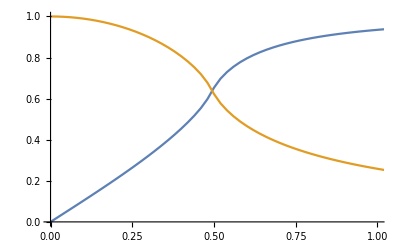

```mathematica
szplot=Table[{ii/50.-1/50.,sz[[ii]]},{ii,1,sites}];
sxxplot=Table[{ii/50.-1/50.,sxx[[ii]]},{ii,1,sites}];
ListLinePlot[{szplot,sxxplot},PlotRange->{{0,1},{0,1}}]
```